```mathematica
(* ===Genesis Closure Scan:Toy Three-Layer Model===*)(*Scan band around current closure value*)ngCenter=1.15428;
ngRange=0.0005;
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

(*Map ng->alpha*)
alphaOf[ng_]:=ng^2-1;

(*Layer-preferred values from earlier exploration*)
ngEFTTarget=1.1539800017415;       (*EFT-preferred ng*)
ngCosmoTarget=1.15428;               (*cosmology/closure value*)
ngObsTarget=1.154307344136304;     (*observer-window preferred ng*)
```

```mathematica
(*Simple quadratic penalties around each layer's target*)CEFT[ng_]:=(ng-ngEFTTarget)^2;
Ccosmo[ng_]:=(ng-ngCosmoTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;
```

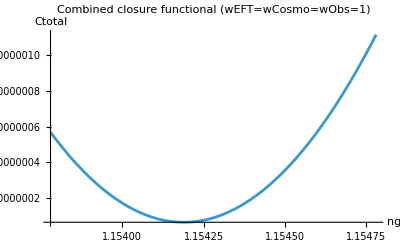

{1.15419,6.59688×10^-8}

```mathematica
(*Initial weights:treat all three layers equally*)wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

(*Visualize total cost*)
baselinePlot=Plot[Ctotal[ng],{ng,ngMin,ngMax},PlotRange->All,AxesLabel->{"ng","Ctotal"},PlotLabel->"Combined closure functional (wEFT=wCosmo=wObs=1)"];

baselinePlot

(*Find minimizing ng in this band*)
baselineMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarBase=ng/. Last[baselineMin];
costStarBase=First[baselineMin];

{ngStarBase,costStarBase}
```

```mathematica
(* ===EFT-emphasized scan===*)wEFT=3.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

eftMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarEFT=ng/. Last[eftMin];
costStarEFT=First[eftMin];

{ngStarEFT,costStarEFT}

(* ===Observer-emphasized scan===*)
wEFT=1.0;
wCosmo=1.0;
wObs=3.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

obsMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarObs=ng/. Last[obsMin];
costStarObs=First[obsMin];

{ngStarObs,costStarObs}
```

{1.15411,1.18443×10^-7}

{1.15424,8.27403×10^-8}

```mathematica
resultsTable={{"Case","wEFT","wCosmo","wObs","ng*","Ctotal(ng*)"},{"Baseline",1.0,1.0,1.0,ngStarBase,costStarBase},{"EFT-heavy",3.0,1.0,1.0,ngStarEFT,costStarEFT},{"Observer-heavy",1.0,1.0,3.0,ngStarObs,costStarObs}};

Grid[resultsTable,Frame->All]
```

Case | wEFT | wCosmo | wObs | ng* | Ctotal(ng*)
Baseline | 1. | 1. | 1. | 1.15419 | 6.59688×10^-8
EFT-heavy | 3. | 1. | 1. | 1.15411 | 1.18443×10^-7
Observer-heavy | 1. | 1. | 3. | 1.15424 | 8.27403×10^-8

```mathematica
(*Given ng,compute model residual for a single galaxy*)GalaxyMisfit[galaxyID_,ng_]:=Module[{alpha=ng^2-1,(*load or access galaxy data here*),(*compute model rotation curve using your Grover law with this alpha*),(*compare to observed SPARC curve*)chi2},chi2];
```

```mathematica
SPARCGalaxies={...};  (*list of galaxy IDs you want to include*)

CosmoMisfit[ng_]:=Total[GalaxyMisfit[#,ng]&/@SPARCGalaxies];
```

```mathematica
(*Use the real SPARC-based misfit*)Ccosmo[ng_]:=CosmoMisfit[ng];
```

```mathematica
(*Scan band*)ngCenter=1.15428;
ngRange=0.0005;
ngMin=ngCenter-ngRange;
ngMax=ngCenter+ngRange;

(*Layer targets unchanged*)
ngEFTTarget=1.1539800017415;
ngObsTarget=1.154307344136304;

CEFT[ng_]:=(ng-ngEFTTarget)^2;
Cobs[ng_]:=(ng-ngObsTarget)^2;

(*Real cosmology misfit from SPARC/Grover notebook*)
Ccosmo[ng_]:=CosmoMisfit[ng];

(*Start with equal weights*)
wEFT=1.0;
wCosmo=1.0;
wObs=1.0;

Ctotal[ng_]:=wEFT*CEFT[ng]+wCosmo*Ccosmo[ng]+wObs*Cobs[ng];

combinedMin=NMinimize[{Ctotal[ng],ngMin<=ng<=ngMax},ng];
ngStarReal=ng/. Last[combinedMin];
costReal=First[combinedMin];

{ngStarReal,costReal}
```

```mathematica
(*DDO 154 toy target (update this number once you re-fit it properly)*)ngDDO154Target=1.15428;

(*Define a per-galaxy misfit as a simple quadratic around that target*)
Cddo154[ng_]:=(ng-ngDDO154Target)^2;

(*Use this as a stand-in for Ccosmo for now*)
Ccosmo[ng_]:=Cddo154[ng];
```

```mathematica
1.15428
```

1.15428